```mathematica
FFx[n_] := Sum[ MoebiusMu[j](1-FFx[n/j]),{j,2,n}]
DiscretePlot[FFx[n],{n,2,100}]
FFp[n_] := Sum[ (1-FFp[n/j]),{j,2,n}]
DiscretePlot[FFp[n],{n,2,100}]
FFy[n_,k_] := Sum[ MoebiusMu[j](1/k-FFy[n/j,k+1]),{j,2,n}]
DiscretePlot[FFy[n,1],{n,2,100}]
FFt[n_,k_] := Sum[ (1/k-FFt[n/j,k+1]),{j,2,n}]
DiscretePlot[FFt[n,1],{n,2,100}]


FFr[n_,k_] := Sum[ (-1/k+FFr[n/j,k+1]),{j,2,n}]
DiscretePlot[FFr[n,1],{n,2,100}]
FFt[n_,k_] := Sum[ (1/k-FFt[n/j,k+1]),{j,2,n}]
DiscretePlot[FFt[n,1],{n,2,100}]
```

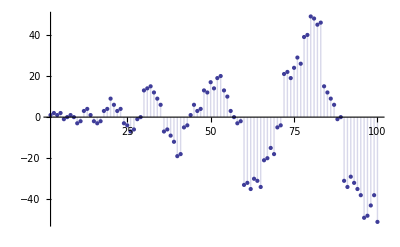

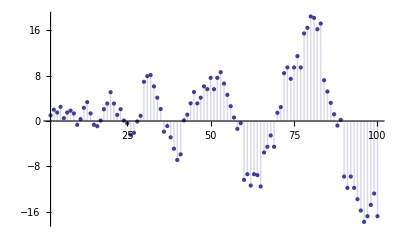

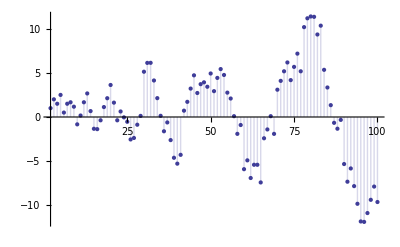

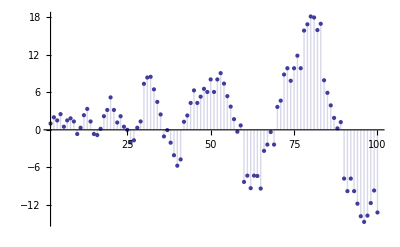

```mathematica
FF[n_] := Sum[ MoebiusMu[j](-1+FF[n/j]),{j,2,n}]
DiscretePlot[FF[n],{n,2,100}]
FF2[n_,k_] := Sum[ MoebiusMu[j](-1/k+FF2[n/j,k+1]),{j,2,n}]
DiscretePlot[FF2[n,1],{n,2,100}]
FF2a[n_,k_] := Sum[ MoebiusMu[j](-1/(k!)+FF2a[n/j,k+1]),{j,2,n}]
DiscretePlot[FF2a[n,1],{n,2,100}]
GG[n_] := Sum[ MangoldtLambda[j]/Log[j](1-GG[Floor[n/j]]),{j,2,n}]
DiscretePlot[GG[n],{n,2,100}]
```

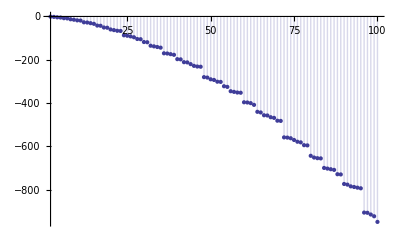

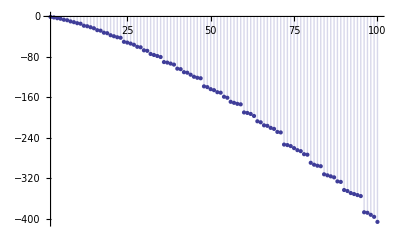

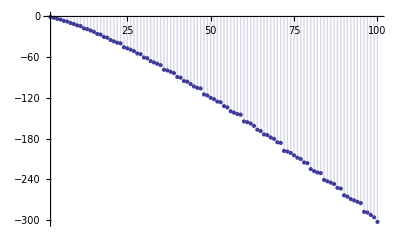

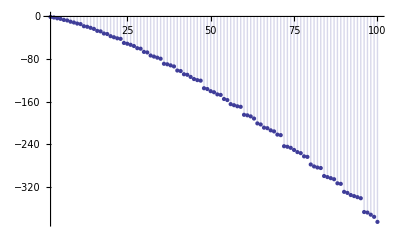

```mathematica
FFa[n_,k_] := Sum[ (-1+FFa[n/j,k+1]),{j,2,n}]
DiscretePlot[FFa[n,1],{n,2,100}]
FFr[n_,k_] := Sum[ (-1/k+FFr[n/j,k+1]),{j,2,n}]
DiscretePlot[FFr[n,1],{n,2,100}]
FFe[n_,k_] := Sum[ (-1/(k!)+FFe[n/j,k+1]),{j,2,n}]
DiscretePlot[FFe[n,1],{n,2,100}]
GG2[n_] := Sum[ MangoldtLambda[j]/Log[j](-1+GG2[Floor[n/j]]),{j,2,n}]
DiscretePlot[GG2[n],{n,2,100}]
```

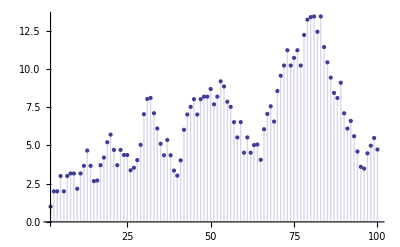

```mathematica
GG3[n_,k_] := Sum[ MangoldtLambda[j]/Log[j](1/k-GG3[Floor[n/j],k+1]),{j,2,n}]
DiscretePlot[GG3[n,1],{n,2,100}]
```